# Zeeman Effect

## on free electron and Fine structure Hydrogen

## Constant Declaration

```mathematica
e=1.60217646 10^-19 ;(* Coulumb *)
ϵ0 = 8.854187817 10^-12;
ℏ=1.054571628 10^-34 ;(* J s*)
me = 9.10938188 10^-31 ;(* kg *)
c = 299792458;
mp=1.672621637 10^-27 ;
gp=5.585694713;
ge=-2.00231904622;
α=e^2/((4π ϵ0)ℏ c);
a=ℏ/(me c α);
μ0=1/(ϵ0 c^2);
μB= (e ℏ)/(2 me);
μN=(e ℏ)/(2mp);
```

```mathematica
α^2 10^6
```

53.2514

## Free Eelctron

```mathematica
Hup[B_]=-ge μB 1/2  B;
Hdn[B_]=ge μB 1/2  B;
```

```mathematica
Hup[B] 1/e 10^6
```

57.9509 B

```mathematica
Manipulate[
Show[
Plot[{Hup[B] 1/(ℏ 2π 10^9),Hdn[B] 1/(ℏ 2π 10^9)}(* in GHz*),{B,0,1},PlotStyle->{Red, Blue}],
Graphics[{Arrow[{{H,Hup[H] 1/(ℏ 2π 10^9)},{H,Hdn[H] 1/(ℏ 2π 10^9)}}],Text[{H,(Hup[H]-Hdn[H])1/(ℏ 2π 10^9)},{H+0.1,Hup[H] 1/(ℏ 4π 10^9)},{-1,-1}]}]

],{{H,0.3},0,1}]
```

```mathematica
Manipulate[
Show[
Plot[{Hup[B] 1/e 10^6,Hdn[B] 1/e 10^6}(* in μeV*),{B,0,1},PlotStyle->{Red, Blue}],
Graphics[{Arrow[{{H,Hup[H] 1/e 10^6},{H,Hdn[H] 1/e 10^6}}],Text[{H,(Hup[H]-Hdn[H])1/e 10^6},{H+0.1,Hup[H] 1/(2e)10^6},{-1,-1}]}]

],{{H,0.3},0,1}]
```

## Bohr Hydrogen

```mathematica
EBohr[n_]:=-1/2(e^2/(4 π ϵ0))^2 me/ℏ^2 1/n^2 (* in J *)
```

```mathematica
(* the energy splitting is due to the orbit angluar momentum*)
(* H = - *)
EOL[n_,m_,B_]:=(e ℏ)/(2me) m B
```

```mathematica
EBohr[2] 1/e
EOL[2,1,B] 1/e 10^6
```

-3.40142

57.8838 B

```mathematica
Manipulate[DiscretePlot[EBohr[n] 1/e+EOL[n,m,B] 1/e,{m,-n+1,n-1},PlotMarkers->{"---",Large},PlotRange->{EBohr[n] 1/e-10^-4,EBohr[n] 1/e+10^-4}],{n,1,4,1},{B,0,1}]
```

```mathematica
Manipulate[Plot[Table[EBohr[n] 1/e+EOL[n,m,B] 1/e,{m,-n+1,n-1}],{B,0,1}],{n,1,4,1}]
```

## Fine Structure Hydrogen

### Hamiltonian of fine structure

```mathematica
HRel=-1/(8 me^3 c^2)P^4
HDarwin=ℏ^3/(8 me^2 c^2)4π α δ[r]
HLS=α ℏ ge/(4 me^2 c)1/r^3 L.S
```

-1.83993×10^72 P^4

1.80258×10^-61 δ[r]

-(1.54852×10^15 L.S)/r^3

```mathematica
Clear[HRel,HDarwin,HLS]
```

### Energy of Zero Field

```mathematica
EBohr[n_]:=-1/2 me α^2 c^2 1/n^2 (* in J *)
Efine[n_,j_]:=EBohr[n]-EBohr[n]^2/(me c^2)((2n)/(j+1/2)-3/2)(* in J*)
(*or *)
ERel[n_,l_]:=-EBohr[n]^2/(2 me c^2)(4 n/(l+1/2)-3)
EDarwin[n_,l_]:=2 n/(me c^2)EBohr[n]^2 KroneckerDelta[0,l]
ESL[n_,j_,l_]:=If[l>0, ge/2 EBohr[n]^2/(me c^2)n(j(j+1)-l(l+1)-3/4)/(l(l+1/2)(l+1)),0]
```

```mathematica
Efine[1,1/2]
EBohr[1]+ERel[1,0]+EDarwin[1,0]+ESL[1,1/2,0]
```

-2.1799×10^-18

-2.1799×10^-18

## Under B - field

```mathematica
(* the Relatibistic term and Darwin Term won't change *)
(* the spin-orbital term will change *)
(* for a field Strength is larger *)
```

### Weak Field

```mathematica
ESL[n_,j_,l_]:=If[l>0, α ℏ 2/(4 me^2 c)ℏ^2/(n^3 a^3)(j(j+1)-l(l+1)-3/4)/(2l(l+1/2)(l+1)),0]
EB[B_,j_,mj_,l_]:=-B μB mj((j(j+1)-3/4+l(l+1))/(2j(j+1))+2(j(j+1)+3/4-l(l+1))/(2j(j+1)))
```

```mathematica
K[j_,l_,g_]:=((j(j+1)-3/4+l(l+1))/(2j(j+1))+g(j(j+1)+3/4-l(l+1))/(2j(j+1)))//Simplify
```

```mathematica
K[k+1/2,k,g]//FullSimplify
K[k-1/2,k,g]//FullSimplify
K[1/2,0,2]//FullSimplify
```

(g+2 k)/(1+2 k)

1+(1-g)/(1+2 k)

2

```mathematica
Table[{K[l+1/2,l,2],K[l-1/2,l,2]},{l,0,5}]
```

{{2,0},{4/3,2/3},{6/5,4/5},{8/7,6/7},{10/9,8/9},{12/11,10/11}}

```mathematica
ESL[2,3/2,1] 1/e 10^6
ESL[2,1/2,1] 1/e 10^6
```

15.0942

-30.1884

```mathematica
EB[B,0+1/2 ,mj,0] 1/e 10^6//FullSimplify
```

-115.768 B mj

```mathematica
μB/e 10^6
```

57.8838

```mathematica
ESL[2,3/2,1] 1/e 10^6+EB[B,3/2,3/2,1] 1/e 10^6
ESL[2,3/2,1] 1/e 10^6+EB[B,3/2,-3/2,1] 1/e 10^6
```

15.0942-115.768 B

15.0942+115.768 B

```mathematica
Table[EB[B,j,mj,l] 1/(B μB mj),{l,1,3},{j,l-1/2,l+1/2}]
```

{{-0.666667,-1.33333},{-0.8,-1.2},{-0.857143,-1.14286}}

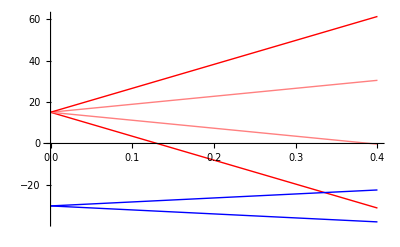

```mathematica
Plot[
{ESL[2,3/2,1] 1/e 10^6+EB[B,3/2,3/2,1] 1/e 10^6,
ESL[2,3/2,1] 1/e 10^6+EB[B,3/2,1/2,1] 1/e 10^6,
ESL[2,3/2,1] 1/e 10^6+EB[B,3/2,-1/2,1] 1/e 10^6,
ESL[2,3/2,1] 1/e 10^6+EB[B,3/2,-3/2,1] 1/e 10^6,
ESL[2,1/2,1] 1/e 10^6+EB[B,1/2,1/2,1] 1/e 10^6,
ESL[2,1/2,1] 1/e 10^6+EB[B,1/2,-1/2,1] 1/e 10^6},{B,0,0.4},PlotStyle->{Red,Pink,Pink,Red, Blue, Blue}]
```

### Strong Field

```mathematica
ESLS[n_,l_,ml_,ms_]:=If[l>0, α ℏ 2/(4 me^2 c)ℏ^2/(n^3 a^3)(ml  ms)/(l(l+1/2)(l+1)),0]
EBS[B_,ml_,ms_]:=-B μB(ml+2ms)
```

```mathematica
ESLS[2,1,1,1/2] 1/e 10^6
ESLS[2,1,1,-1/2] 1/e 10^6
EBS[1,1,1/2] 1/e 10^6
```

15.0942

-15.0942

-115.768

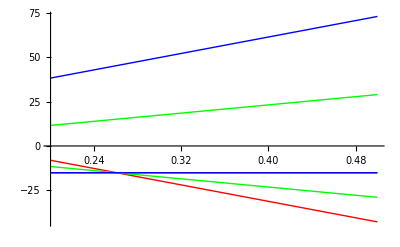

```mathematica
Plot[
{ESLS[2,1,1,1/2] 1/e 10^6+EBS[B,1,1/2] 1/e 10^6,
ESLS[2,1,1,-1/2] 1/e 10^6+EBS[B,1,-1/2] 1/e 10^6,
ESLS[2,1,0,1/2] 1/e 10^6+EBS[B,0,1/2] 1/e 10^6,
ESLS[2,1,0,-1/2] 1/e 10^6+EBS[B,0,-1/2] 1/e 10^6,
ESLS[2,1,-1,1/2] 1/e 10^6+EBS[B,-1,1/2] 1/e 10^6,
ESLS[2,1,-1,-1/2] 1/e 10^6+EBS[B,-1,-1/2] 1/e 10^6},{B,0.2,0.5},PlotStyle->{Red,Red,Green,Green, Blue, Blue}]
```